```mathematica
<< NC`
```

You are using the version of NCAlgebra which is found in:

C:\Users\Matthew Thornton\NC\

You can now use "<< NCAlgebra`" to load NCAlgebra.

```mathematica
<<NCAlgebra`
```

------------------------------------------------------------
NCAlgebra - Version 5.0.4
Compatible with Mathematica Version 10 and above

Authors:

  J. William Helton*
  Mauricio de Oliveira&

* Math, UCSD, La Jolla, CA
& MAE, UCSD, La Jolla, CA

with major earlier contributions by:

  Mark Stankus$ 
  Robert L. Miller#

$ Math, Cal Poly San Luis Obispo
# General Atomics Corp

Copyright: 
  Helton and de Oliveira 2017
  Helton 2002
  Helton and Miller June 1991
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.

Current primary support is from the 
  NSF Division of Mathematical Sciences.
  
This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.

For NCAlgebra updates see:

  www.github.com/NCAlgebra/NC
  www.math.ucsd.edu/~ncalg

------------------------------------------------------------

```mathematica
SetNonCommutative[a, b, ad, bd]
SetCommutative[σ4, σ3, σ1, σ2, σ5, γ1, γ2]
```

```mathematica
xh2[x_]:= x ** h2
h2x[x_]:=  h2 **x
adxa[x_]:=  a** x **ad
xada[x_]:=x**ad**a
adax[x_]:=ad ** a ** x
bdxb[x_]:=b ** x ** bd
xbdb[x_]:=x ** bd ** b
bdbx[x_]:= bd ** b **x
```

```mathematica
dtx[x_]:=ⅈ xh2[x] - ⅈ h2x[x] + γ1(adxa[x] - (0.5)xada[x] - (0.5)adax[x]) + γ2 ( bdxb[x] - (0.5)xbdb[x] - (0.5)bdbx[x])
```

```mathematica
dtx[a]
```

γ1 (-a**a**ad-0.5 a**ad**a-0.5 ad**a**a)+γ2 (-0.5 a**bd**b-b**a**bd-0.5 bd**b**a)

```mathematica
commutators = {
a ** ad -> 1 + ad ** a,
b ** bd -> 1 + bd ** b,
b**a -> a**b,
a ** bd -> bd ** a,
b ** ad -> ad ** b,
bd ** ad-> ad**bd
}
```

{a**ad→1+ad**a,b**bd→1+bd**b,b**a→a**b,a**bd→bd**a,b**ad→ad**b,bd**ad→ad**bd}

```mathematica
h2 = (
σ4 bd ** a ** bd ** a + σ5 bd **a ** (ad ** a - bd ** b - 1) 
+ σ4 ad ** b ** ad ** b + σ5 ad ** b ** (ad **a  - bd ** b -1)
+ σ1 ( bd ** b ** bd ** b + ad ** a ** ad ** a) + σ2 ( ad ** a ** bd **b) + σ3(ad ** a + bd **b)
)
```

σ3 (ad**a+bd**b)+σ5 ad**b**(-1+ad**a-bd**b)+σ5 bd**a**(-1+ad**a-bd**b)+σ2 ad**a**bd**b+σ4 ad**b**ad**b+σ4 bd**a**bd**a+σ1 (ad**a**ad**a+bd**b**bd**b)

```mathematica
evals[x_]:=Module[{expression, flag, n},
flag=True;
expression=.;
expression[1] = dtx[x];
n=1;
While[flag, 
n=n+1;
expression[n] = NCReplaceAll[expression[n-1], commutators]//NCExpand;
If[
expression[n]==expression[n-1],
flag = False
]
];
expression[n]
]
```

```mathematica
evals[a]
(* These evals look weird - the γ terms are positive rather than negative... *)
```

-2.5 a γ1-a γ2+ⅈ a σ1+ⅈ a σ3-2 ⅈ b σ5-2. γ1 ad**a**a+2 ⅈ σ1 ad**a**a+2 ⅈ σ5 ad**a**b+2 ⅈ σ4 ad**b**b+ⅈ σ5 bd**a**a-2. γ2 bd**a**b+ⅈ σ2 bd**a**b-ⅈ σ5 bd**b**b

```mathematica
fullcommute[x_]:=Module[{expression, flag, n},
flag = True;
expression=.;
expression[1] = x;
n=1;
While[flag,
n=n+1;
expression[n] = NCReplaceAll[expression[n-1], commutators]//NCExpand;
If[
expression[n]==expression[n-1],
flag=False;
]
];
expression[n]
]
```

### Linearizing

```mathematica
twolinear[x_?StringQ, y_?StringQ]:=
x<>y<>"[t]"
threelinear[x_?StringQ,y_?StringQ, z_?StringQ]:=
x<>"[t] "<> y<>z<>"[t] + "<> y<>"[t] "<>x<>z<>"[t] + "<>z<>"[t] "<>x<>y<>"[t] - 2 "<>x<>"[t] "<>y<>"[t] "<>z<>"[t]"
fourlinear[w_?StringQ,x_?StringQ,y_?StringQ, z_?StringQ]:=
w<>x<>"[t] "<> y<>z<>"[t] + "<>w<> y<>"[t] "<>x<>z<>"[t] + "<>w<>z<>"[t] "<>x<>y<>"[t] - 2 "<>w<>"[t] "<>x<>"[t] "<>y<>"[t] "<>z<>"[t]"
fivelinear[a_?StringQ ,b_?StringQ, c_?StringQ, d_?StringQ, e_?StringQ]:=
a<>"[t] "<>b<>c<>"[t] "<>d<>e<>"[t] +"<>
a<>"[t] "<>b<>d<>"[t] "<>c<>e<>"[t] + "<>
a<>"[t] "<>b<>e<>"[t] "<>c<>d<>"[t] + " <>
b<>"[t] "<>a<>c<>"[t] "<>d<>e<>"[t] + "<>
b<>"[t] "<>a<>d<>"[t] "<>c<>e<>"[t] + "<>
b<>"[t] "<>a<>e<>"[t] "<>c<>d<>"[t] + "<>
c<>"[t] "<>a<>b<>"[t] "<>d<>e<>"[t] + "<>
c<>"[t] "<>a<>d<>"[t] "<>b<>e<>"[t] + "<>
c<>"[t] "<>a<>e<>"[t] "<>b<>d<>"[t] + "<>
d<>"[t] "<>a<>b<>"[t] "<>c<>e<>"[t] + "<>
d<>"[t] "<>a<>c<>"[t] "<>b<>e<>"[t] + "<>
d<>"[t] "<>a<>e<>"[t] "<>b<>c<>"[t] + "<>
e<>"[t] "<>a<>b<>"[t] "<>c<>d<>"[t] + "<>
e<>"[t] "<>a<>c<>"[t] "<>b<>d<>"[t] + "<>
e<>"[t] "<>a<>d<>"[t] "<>b<>c<>"[t] + "<>
"-2 ( "<>
a<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] +"<>
a<>c<>"[t] "<>b<>"[t] "<>d <>"[t] "<>e<>"[t] + "<>
a<>d<>"[t] "<>b<>"[t] "<>c<>"[t] "<>e<>"[t] + "<>
a<>e<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] + "<>
b<>c<>"[t] "<>a<>"[t] "<>d<>"[t] "<>e<>"[t] + "<>
b<>d<>"[t] "<>a<>"[t] "<>c<>"[t] "<> e<>"[t] + "<>
b<>e<>"[t] "<>a<>"[t] "<> c<>"[t] "<>d<>"[t] + "<>
c<>d<>"[t] "<>a<>"[t] "<>b<>"[t] "<>e<>"[t] + "<>
c<>e<>"[t] "<>a<>"[t] "<>b<>"[t] "<>d<>"[t] + "<>
d<>e<>"[t] "<>a<>"[t] "<>b<>"[t] "<>c<>"[t]) +
6 "<>a<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] "
sixlinear[a_?StringQ, b_?StringQ, c_?StringQ, d_?StringQ, e_?StringQ, f_?StringQ]:=
a<>b<>"[t] "<>c<>d<>"[t] "<>e<>f<>"[t] + "<> a<>b<>"[t] "<>c<>e<>"[t] "<>d<>f<>"[t] +  "<> a<>b<>"[t] "<>c<>f<>"[t] "<>d<>e<>"[t] + "<> a<>c<>"[t] "<>b<>d<>"[t] "<>e<>f<>"[t] + "<> a<>c<>"[t] "<>b<>e<>"[t] "<>d<>f<>"[t] + "<> a<>c<>"[t] "<>b<>f<>"[t] "<>d<>e<>"[t] + "<> a<>
d<>"[t] "<>b<>c<>"[t] "<>e<>f<>"[t] + "<> a<>d<>"[t] "<>b<>e<>"[t] "<>c<>f<>"[t] + "<>a<>d<>"[t] "<>b<>f<>"[t] "<>c<>e<>"[t] + "<> a<>e<>"[t] "<>b<>c<>"[t] "<>d<>f<>"[t] + "<>  a<>e<>"[t] "<>b<>d<>"[t] "<>c<>f<>"[t] + "<> a<>e<>"[t] "<>b<>f<>"[t] "<>c<>d<>"[t] + "<> a<>f<>"[t] "<>b<>c<>"[t] "<>d<>e<>"[t] + "<> a<>f<>"[t] "<>b<>d<>"[t] "<>c<>e<>"[t] + "<> a<>f<>"[t] "<>b<>e<>"[t] "<>c<>d<>"[t] -2("<> a<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> a<>c<>"[t] "<>b<>"[t] "<>d<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> a<>d<>"[t] "<>b<>"[t] "<>c<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> a<>e<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>f<>"[t] + "<> a<>f<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] + "<> b<>c<>"[t] "<>a<>"[t] "<>d<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> b<>d<>"[t] "<>a<>"[t] "<>c<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> b<>e<>"[t] "<>a<>"[t] "<>c<>"[t] "<>d<>"[t] "<>f<>"[t] + "<> b<>f<>"[t] "<>a<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] + "<> c<>d<>"[t] "<>a<>"[t] "<>b<>"[t] "<>e<>"[t] "<>f<>"[t] + "<> c<>e<>"[t] "<>a<>"[t] "<>b<>"[t] "<>d<>"[t] "<>f<>"[t] + "<> c<>f<>"[t] "<>a<>"[t] "<>b<>"[t] "<>d<>"[t] "<>e<>"[t] + "<> d<>e<>"[t] "<>a<>"[t] "<>b<>"[t] "<>c<>"[t] "<>f<>"[t]  + "<> d<>f<>"[t] "<>a<>"[t] "<>b<>"[t] "<>c<>"[t] "<>e<>"[t] + "<>
e<>f<>"[t] "<>a<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] ) + 16 "<>a<>"[t] "<>b<>"[t] "<>c<>"[t] "<>d<>"[t] "<>e<>"[t] "<>f<>"[t] "
```

```mathematica
orderonereplacements=
{"ad"->"ad[t]",  "a"->"a[t]" , "bd"->"bd[t]","b"->"b[t]"};

ordertworeplacements=Module[
{listperms, listperms2, listperms3,listpermsReplacements},
listperms = Permutations[
{"ad", "ad","bd", "bd",  "a", "a", "b", "b"},{2}
];
listperms2= Table[
fullcommute[ToExpression[listperms[[i, 1]]<>" ** "<>listperms[[i,2]]]],
{i, 1, Length[listperms]}]//DeleteDuplicates;
listperms3 = 
StringReplace[Table[
listperms2[[i]]//ToString
,
{i, 1, Length[listperms2]}
],
{"1 + ad ** a "->" ad ** a ",
"1 + bd ** b "-> " bd ** b "}
];
listpermsReplacements = Table[
listperms3[[i]]->StringCases[
listperms3[[i]], x__~~" ** "~~ y__ :>twolinear[x,y]
][[1]],
{i, 1, Length[listperms3]}
];
listpermsReplacements
];


orderthreereplacements = Module[
{listperms, listperms2, listperms3, listpermsReplacements},
listperms = Permutations[
{"ad", "ad", "ad","bd", "bd", "bd",  "a", "a", "a", "b", "b", "b"},{3}
];
listperms2= Table[
fullcommute[ToExpression[listperms[[i, 1]]<>" ** "<>listperms[[i,2]]<>" ** "<>listperms[[i,3]]]],
{i, 1, Length[listperms]}]//DeleteDuplicates;

listperms3 = 
Table[
listperms2[[i]]//ToString
,
{i, 1, Length[listperms2]}
];
listpermsReplacements = Table[
listperms3[[i]]->StringCases[
listperms3[[i]], x__~~" ** "~~ y__ ~~ " ** "~~z__:>threelinear[x,y,z]
][[1]],
{i, 1, Length[listperms3]}
];
listpermsReplacements
];


orderfourreplacements = Module[
{listperms, listperms2, listperms3, listpermsReplacements},
listperms = Permutations[
{"ad", "ad", "ad", "ad","bd", "bd", "bd", "bd",  "a", "a", "a", "a", "b", "b", "b", "b"},{4}
];
listperms2= Table[
fullcommute[ToExpression[listperms[[i, 1]]<>" ** "<>listperms[[i,2]]<>" ** "<>listperms[[i,3]]<>" ** "<>listperms[[i,4]]]],
{i, 1, Length[listperms]}]//DeleteDuplicates;

listperms3 = 
StringReplace[Table[
listperms2[[i]]//ToString
,
{i, 1, Length[listperms2]}
],
{"1 + ad ** a "->"ad ** a "}];
listpermsReplacements = Table[
listperms3[[i]]->StringCases[
listperms3[[i]], w__~~" ** "~~x__~~" ** "~~ y__ ~~ " ** "~~z__:>fourlinear[w,x,y,z]
][[1]],
{i, 1, Length[listperms3]}
];
listpermsReplacements
];


orderfivereplacements = Module[
{listperms, listperms2, listperms3, listpermsReplacements},
listperms = Permutations[
{"ad", "ad", "ad", "ad", "ad","bd", "bd", "bd", "bd", "bd",  "a", "a", "a", "a", "a", "b", "b", "b", "b", "b"},{5}
];
listperms2= Table[
fullcommute[ToExpression[listperms[[i, 1]]<>" ** "<>listperms[[i,2]]<>" ** "<>listperms[[i,3]]<>" ** "<>listperms[[i,4]]<> " ** "<>listperms[[i,5]]]],
{i, 1, Length[listperms]}]//DeleteDuplicates;

listperms3 = 
StringReplace[Table[
listperms2[[i]]//ToString
,
{i, 1, Length[listperms2]}
],{}];
listpermsReplacements = Table[
listperms3[[i]]->StringCases[
listperms3[[i]], a__~~" ** "~~b__~~" ** "~~ c__ ~~ " ** "~~d__~~" ** "~~e__:>fivelinear[a, b, c, d, e]
][[1]],
{i, 1, Length[listperms3]}
];
listpermsReplacements
];


ordersixreplacements = Module[
{listperms, listperms2, listperms3, listpermsReplacements},
listperms = Permutations[
{"ad", "ad", "ad", "ad", "ad", "ad","bd", "bd", "bd", "bd", "bd", "a", "a", "a", "a", "a", "a", "b", "b", "b", "b", "b", "b"},{6}
];
listperms2= Table[
fullcommute[ToExpression[listperms[[i, 1]]<>" ** "<>listperms[[i,2]]<>" ** "<>listperms[[i,3]]<>" ** "<>listperms[[i,4]]<> " ** "<>listperms[[i,5]]<> " ** "<>listperms[[i,6]]]],
{i, 1, Length[listperms]}]//DeleteDuplicates;

listperms3 = 
StringReplace[Table[
listperms2[[i]]//ToString
,
{i, 1, Length[listperms2]}
],{}];
listpermsReplacements = Table[
listperms3[[i]]->StringCases[
listperms3[[i]], a__~~" ** "~~b__~~" ** "~~ c__ ~~ " ** "~~d__~~" ** "~~e__~~" ** "~~f__:>sixlinear[a, b, c, d, e,f]
][[1]],
{i, 1, Length[listperms3]}
];
listpermsReplacements
];
```

### Actually linearizing

```mathematica
allreplacements = Flatten@Join[{ordersixreplacements, orderfivereplacements,orderfourreplacements, orderthreereplacements, ordertworeplacements, orderonereplacements}];
```

```mathematica
tostringWithCoefficients[item_]:=
Module[{commlist, noncommlist,coefficients, len},
commlist = {};
noncommlist = {};
len = Length[item];
Table[
If[
CommutativeQ[item[[j]]],
AppendTo[commlist, item[[j]]]
,
AppendTo[noncommlist, item[[j]]]
],
 {j, 1 , len}
];
coefficients = Apply[Times, commlist, {0}];
If[Length[noncommlist]==0,
noncommlist={1}];
ToString[coefficients]<>"( "<>ToString[noncommlist[[1]]] <>")"
]
```

```mathematica
evals2string[operator_]:=
Module[{tabout, tabout2, tabout3, eqn1,eqns2,  length, eqns3},
eqn1 = evals[operator];
length = Length[eqn1];
tabout = Table[
tostringWithCoefficients[eqn1[[i]]],
{i, 1, length}
];

tabout2 = Riffle[
tabout, {" + "}
];

eqns2 = StringJoin[tabout2];

eqns3 = StringReplace[eqns2, allreplacements];

eqns3
]
```

```mathematica
evals2string[ad**a]
```

-γ1( 1) + -4. γ1( ada[t]) + -γ2( ada[t]) + (-2 I) σ5( adb[t]) + -2. γ1( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ2( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])

```mathematica
evals2string[bd**b]
```

-γ2( 1) + (2 I) σ5( adb[t]) + -γ1( bdb[t]) + -4. γ2( bdb[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ1( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -2. γ2( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])

```mathematica
evals[ad**a]
```

-γ1-4. γ1 ad**a-γ2 ad**a-2 ⅈ σ5 ad**b-2. γ1 ad**ad**a**a+ⅈ σ5 ad**ad**a**b+2 ⅈ σ4 ad**ad**b**b-ⅈ σ5 ad**bd**a**a-2. γ2 ad**bd**a**b-ⅈ σ5 ad**bd**b**b-2 ⅈ σ4 bd**bd**a**a+ⅈ σ5 bd**bd**a**b

```mathematica
stringequations = 
{
"a'[t] == "<>evals2string[a],
"ad'[t] == "<>evals2string[ad],
"b'[t] == "<>evals2string[b],
"bd'[t] == "<>evals2string[bd],
"aa'[t] == "<>evals2string[a**a],
"ada'[t] == "<>evals2string[ad**a],
"adad'[t] == "<>evals2string[ad ** ad],
"bb'[t] == "<>evals2string[b**b],
"bdb'[t] == "<>evals2string[bd **b],
"bdbd'[t] == "<>evals2string[bd*bd],
"ab'[t] == "<>evals2string[a**b],
"adb'[t] == "<>evals2string[ad ** b],
"bda'[t] == "<>evals2string[bd**a],
"adbd'[t] == "<>evals2string[ad ** bd]
}
```

{a'[t] == -2.5 γ1( a[t]) + -γ2( a[t]) + I σ1( a[t]) + I σ3( a[t]) + (-2 I) σ5( b[t]) + -2. γ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ5( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + (2 I) σ4( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + I σ5( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + -2. γ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + I σ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -I σ5( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t]),ad'[t] == -2.5 γ1( ad[t]) + -γ2( ad[t]) + -I σ1( ad[t]) + -I σ3( ad[t]) + -2. γ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + -I σ5( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + (-2 I) σ5( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -2. γ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + -I σ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + (-2 I) σ4( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + I σ5( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t]),b'[t] == -γ1( b[t]) + -2.5 γ2( b[t]) + I σ1( b[t]) + I σ3( b[t]) + I σ5( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + -2. γ1( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + I σ2( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + -I σ5( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + (2 I) σ4( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + (-2 I) σ5( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -2. γ2( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t]) + (2 I) σ1( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t]),bd'[t] == -γ1( bd[t]) + -2.5 γ2( bd[t]) + -I σ1( bd[t]) + -I σ3( bd[t]) + (2 I) σ5( ad[t]) + -I σ5( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ4( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + -2. γ1( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -I σ2( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + (2 I) σ5( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + I σ5( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + -2. γ2( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t]) + (-2 I) σ1( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t]),aa'[t] == -4. γ1( aa[t]) + -γ2( aa[t]) + (4 I) σ1( aa[t]) + (2 I) σ3( aa[t]) + (-2 I) σ5( ab[t]) + (2 I) σ4( bb[t]) + -2. γ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (4 I) σ4( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ5( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -2. γ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (2 I) σ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-2 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]),ada'[t] == -γ1( 1) + -4. γ1( ada[t]) + -γ2( ada[t]) + (-2 I) σ5( adb[t]) + -2. γ1( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ2( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]),adad'[t] == -4. γ1( adad[t]) + -γ2( adad[t]) + (-4 I) σ1( adad[t]) + (-2 I) σ3( adad[t]) + (-2 I) σ5( adbd[t]) + (-2 I) σ4( bdbd[t]) + -2. γ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-4 I) σ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ5( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-4 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -2. γ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-2 I) σ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-4 I) σ4( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (2 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]),bb'[t] == (2 I) σ4( aa[t]) + (-2 I) σ5( ab[t]) + -γ1( bb[t]) + -4. γ2( bb[t]) + (4 I) σ1( bb[t]) + (2 I) σ3( bb[t]) + (2 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + -2. γ1( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ2( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ5( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (4 I) σ4( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-4 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -2. γ2( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t]) + (4 I) σ1( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t]),bdb'[t] == -γ2( 1) + (2 I) σ5( adb[t]) + -γ1( bdb[t]) + -4. γ2( bdb[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ1( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -2. γ2( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t]),bdbd'[t] == (-2 I) σ4( adad[t]) + (6 I) σ5( adbd[t]) + -γ1( bdbd[t]) + -4. γ2( bdbd[t]) + (-4 I) σ1( bdbd[t]) + (-2 I) σ3( bdbd[t]) + (-2 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-4 I) σ4( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -2. γ1( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-2 I) σ2( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (4 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (2 I) σ5( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + -2. γ2( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t]) + (-4 I) σ1( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t]),ab'[t] == I σ5( aa[t]) + -2.5 γ1( ab[t]) + -2.5 γ2( ab[t]) + (2 I) σ1( ab[t]) + I σ2( ab[t]) + (2 I) σ3( ab[t]) + (-3 I) σ5( bb[t]) + I σ5( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + -2. γ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (2 I) σ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ2( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ5( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ4( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (2 I) σ4( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -I σ5( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + -2. γ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + (2 I) σ1( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + I σ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -I σ5( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t]),adb'[t] == -2.5 γ1( adb[t]) + -2.5 γ2( adb[t]) + I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + -2. γ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + I σ2( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ5( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + (2 I) σ4( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (-4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + -2. γ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ1( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + -I σ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t]),bda'[t] == (2 I) σ5( ada[t]) + -2.5 γ1( bda[t]) + -2.5 γ2( bda[t]) + (-2 I) σ5( bdb[t]) + -I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ4( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + -2. γ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (2 I) σ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ2( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ4( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ5( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -2. γ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + (-2 I) σ1( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t]),adbd'[t] == I σ5( adad[t]) + -2.5 γ1( adbd[t]) + -2.5 γ2( adbd[t]) + (-2 I) σ1( adbd[t]) + -I σ2( adbd[t]) + (-2 I) σ3( adbd[t]) + I σ5( bdbd[t]) + -I σ5( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ4( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + -2. γ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-2 I) σ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -I σ2( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + I σ5( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -I σ5( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + -2. γ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ1( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + -I σ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ4( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + I σ5( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])}

## Solving

```mathematica
stringequations = {"a'[t] == -2.5 γ1( a[t]) + -γ2( a[t]) + I σ1( a[t]) + I σ3( a[t]) + (-2 I) σ5( b[t]) + -2. γ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ5( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + (2 I) σ4( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + I σ5( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + -2. γ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + I σ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -I σ5( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","ad'[t] == -2.5 γ1( ad[t]) + -γ2( ad[t]) + -I σ1( ad[t]) + -I σ3( ad[t]) + -2. γ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + -I σ5( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + (-2 I) σ5( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -2. γ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + -I σ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + (-2 I) σ4( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + I σ5( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","b'[t] == -γ1( b[t]) + -2.5 γ2( b[t]) + I σ1( b[t]) + I σ3( b[t]) + I σ5( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + -2. γ1( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + I σ2( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + -I σ5( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + (2 I) σ4( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + (-2 I) σ5( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -2. γ2( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t]) + (2 I) σ1( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","bd'[t] == -γ1( bd[t]) + -2.5 γ2( bd[t]) + -I σ1( bd[t]) + -I σ3( bd[t]) + (2 I) σ5( ad[t]) + -I σ5( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ4( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + -2. γ1( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -I σ2( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + (2 I) σ5( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + I σ5( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + -2. γ2( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t]) + (-2 I) σ1( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","aa'[t] == -4. γ1( aa[t]) + -γ2( aa[t]) + (4 I) σ1( aa[t]) + (2 I) σ3( aa[t]) + (-2 I) σ5( ab[t]) + (2 I) σ4( bb[t]) + -2. γ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (4 I) σ4( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ5( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -2. γ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (2 I) σ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-2 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t])","ada'[t] == -γ1( 1) + -4. γ1( ada[t]) + -γ2( ada[t]) + (-2 I) σ5( adb[t]) + -2. γ1( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ2( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","adad'[t] == -4. γ1( adad[t]) + -γ2( adad[t]) + (-4 I) σ1( adad[t]) + (-2 I) σ3( adad[t]) + (-2 I) σ5( adbd[t]) + (-2 I) σ4( bdbd[t]) + -2. γ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-4 I) σ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ5( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-4 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -2. γ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-2 I) σ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-4 I) σ4( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (2 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t])","bb'[t] == (2 I) σ4( aa[t]) + (-2 I) σ5( ab[t]) + -γ1( bb[t]) + -4. γ2( bb[t]) + (4 I) σ1( bb[t]) + (2 I) σ3( bb[t]) + (2 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + -2. γ1( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ2( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ5( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (4 I) σ4( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-4 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -2. γ2( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t]) + (4 I) σ1( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","bdb'[t] == -γ2( 1) + (2 I) σ5( adb[t]) + -γ1( bdb[t]) + -4. γ2( bdb[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -2. γ1( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -2. γ2( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","bdbd'[t] == (-2 I) σ4( adad[t]) + (6 I) σ5( adbd[t]) + -γ1( bdbd[t]) + -4. γ2( bdbd[t]) + (-4 I) σ1( bdbd[t]) + (-2 I) σ3( bdbd[t]) + (-2 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-4 I) σ4( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -2. γ1( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-2 I) σ2( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (4 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (2 I) σ5( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + -2. γ2( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t]) + (-4 I) σ1( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])","ab'[t] == I σ5( aa[t]) + -2.5 γ1( ab[t]) + -2.5 γ2( ab[t]) + (2 I) σ1( ab[t]) + I σ2( ab[t]) + (2 I) σ3( ab[t]) + (-3 I) σ5( bb[t]) + I σ5( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + -2. γ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (2 I) σ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ2( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ5( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ4( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (2 I) σ4( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -I σ5( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + -2. γ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + (2 I) σ1( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + I σ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -I σ5( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","adb'[t] == -2.5 γ1( adb[t]) + -2.5 γ2( adb[t]) + I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + -2. γ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + I σ2( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ5( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + (2 I) σ4( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (-4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + -2. γ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ1( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + -I σ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","bda'[t] == (2 I) σ5( ada[t]) + -2.5 γ1( bda[t]) + -2.5 γ2( bda[t]) + (-2 I) σ5( bdb[t]) + -I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ4( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + -2. γ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (2 I) σ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ2( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ4( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ5( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -2. γ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + (-2 I) σ1( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","adbd'[t] == I σ5( adad[t]) + -2.5 γ1( adbd[t]) + -2.5 γ2( adbd[t]) + (-2 I) σ1( adbd[t]) + -I σ2( adbd[t]) + (-2 I) σ3( adbd[t]) + I σ5( bdbd[t]) + -I σ5( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ4( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + -2. γ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-2 I) σ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -I σ2( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + I σ5( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -I σ5( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + -2. γ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ1( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + -I σ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ4( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + I σ5( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])"};
```

```mathematica
Quit
```

```mathematica
twomodesolver[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==αin,
b[0] ==0,
ad[0] == Conjugate[αin],
bd[0]==0,
aa[0] == αin^2,
ada[0] == Abs[αin]^2,
adad[0] ==  Conjugate[αin]^2,
bb[0] ==0, 
bdb[0]==0,
bdbd[0]==0,
ab[0]==0,
adb[0]==0,
bda[0]==0,
adbd[0]==0
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax}
][[1]]


]
```

```mathematica
tmax = 0.02;
```

```mathematica
sol700 = twomodesolver[√700, 30, 40, 2.0, 0.0, 400.0, tmax];1;
sol500 = twomodesolver[√500, 30, 40, 2.0, 0.0, 400.0, tmax];1;
sol300 = twomodesolver[√300, 30, 40, 2.0, 0.0, 400.0, tmax];1;
sol100 = twomodesolver[√100, 30, 40, 2.0, 0.0, 400.0, tmax];1;
```

```mathematica
ada[0.01]/.sol100
```

24.9236-0.168769 ⅈ

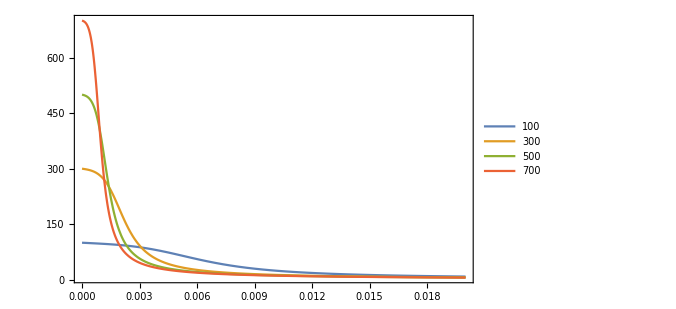

```mathematica
Plot[
{
Re@ada[t]/.sol100,
Re@ada[t]/.sol300,
Re@ada[t]/.sol500,
Re@ada[t]/.sol700
},
{t,0,tmax}, 
PlotRange->All,
PlotLegends->{"100", "300", "500", "700"}, 
Frame->True,
ImageSize->500
]
```

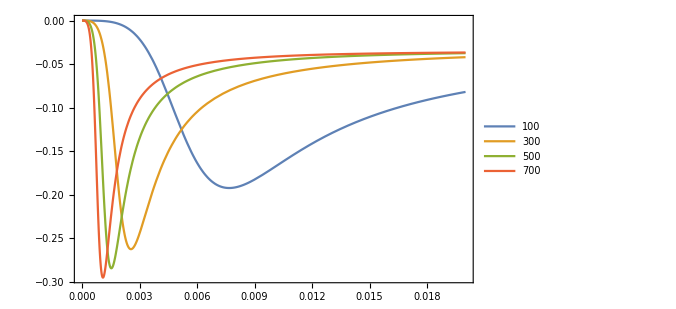

```mathematica
Plot[
{
Im@ada[t]/.sol100,
Im@ada[t]/.sol300,
Im@ada[t]/.sol500,
Im@ada[t]/.sol700
},
{t,0,tmax}, 
PlotRange->All,
PlotLegends->{"100", "300", "500", "700"}, 
Frame->True,
ImageSize->500
]
```